Computational Journey of Quantum Mechanics | Amir H. Ebrahimnezhad | Advisor: Prf. Ebrahim | University of Tehran

# Advanced Topics in Computational Linear Algebra

## Overview

The following notebook serves as a complementary section for the previous one, where we’ve delved into linear algebra from symbolic computational point of view. In this notebook we would briefly introduce decompositions, matrix functions, and structured and sparse matrices. Later we work on extensions to infinite dimensional space, random matrix theory and Bohemian matrices, and lastly discuss multilinear algebra.

This notebook’s can be skipped since the topics might not be needed during other sections, but for the purpose of being a complete journey we shall discuss them.

## Matrix Decomposition

## Shur Decomposition

The Schur decomposition is a fundamental matrix factorization that transforms any square matrix into an upper triangular form through unitary similarity transformations. For any square matrix , the Shur decomposition states that:

where:

is a unitary matrix.

is an upper triangular matrix.

The diagonal elements of  are the eigenvalues of

The significance of this decomposition is in its universality, meaning that there always exists such decomposition for any square matrix, unlike diagonalization which requires a complete set of linearly independent eigenvectors. 

The Schur decomposition essentially provides a best attempt at diagonalization, leaving the matrix in an upper triangular form that reveals the eigen values on the diagonal.

```mathematica
(*Creating a sample matrix*)
A={{2.7,4.8,8.1},{-.6,1,0},{.1,0,.3}};
MatrixForm[A]

(*Computing the Schur decomposition*)
{U,T}=SchurDecomposition[A];

(*Display the factors*)
Print["Unitary matrix U:"]
MatrixForm[U]
Print["Upper triangular matrix T:"]
MatrixForm[T]

(*Verification*)
Print["Verification: A = U.T.U^*"]
MatrixForm[U.T.ConjugateTranspose[U]]
Print["Original matrix A:"]
MatrixForm[A]
Print["Difference:"]
MatrixForm[U.T.ConjugateTranspose[U]-A//Chop]
```

(2.7 | 4.8 | 8.1
-0.6 | 1 | 0
0.1 | 0 | 0.3)

Unitary matrix U:

(-0.969016 | 0.246437 | -0.0166355
0.243801 | 0.965103 | 0.0955848
-0.0396106 | -0.0885675 | 0.995282)

Upper triangular matrix T:

(1.91769 | -4.23924 | -8.19909
0.370608 | 1.91769 | 2.16431
0. | 0. | 0.164614)

Verification: A = U.T.U^*

(2.7 | 4.8 | 8.1
-0.6 | 1. | 1.38778×10^-16
0.1 | -4.51028×10^-17 | 0.3)

Original matrix A:

(2.7 | 4.8 | 8.1
-0.6 | 1 | 0
0.1 | 0 | 0.3)

Difference:

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

### Visualization

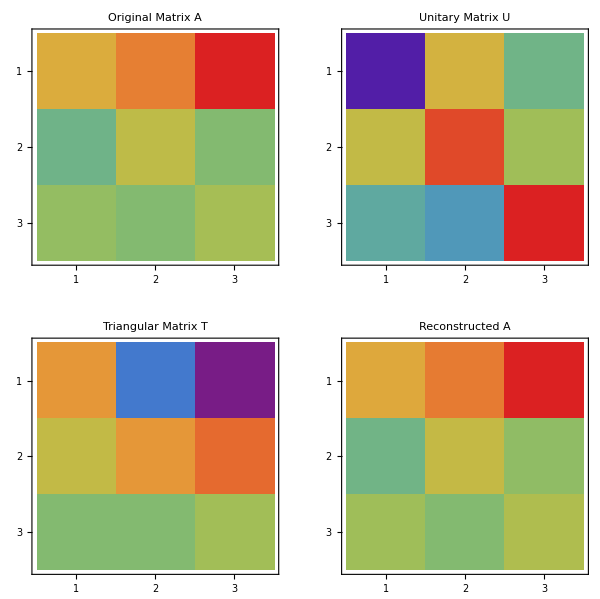

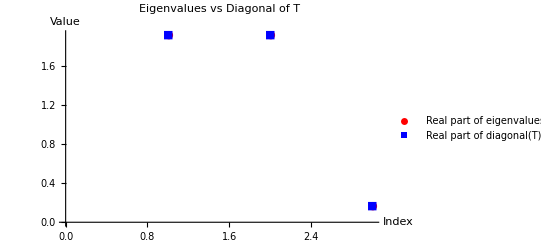

```mathematica
(*Visualization of the Schur decomposition*)
GraphicsGrid[{{MatrixPlot[A,ColorFunction->"Rainbow",PlotLabel->"Original Matrix A"],MatrixPlot[U,ColorFunction->"Rainbow",PlotLabel->"Unitary Matrix U"]},{MatrixPlot[T,ColorFunction->"Rainbow",PlotLabel->"Triangular Matrix T"],MatrixPlot[U.T.ConjugateTranspose[U],ColorFunction->"Rainbow",PlotLabel->"Reconstructed A"]}},ImageSize->600]

(*Visualizing the eigenvalues*)
eigenvalues=Eigenvalues[A];
diagonalT=Diagonal[T];

ListPlot[{Re[eigenvalues],Re[diagonalT]},PlotStyle->{Red,Blue},PlotLegends->{"Real part of eigenvalues","Real part of diagonal(T)"},PlotLabel->"Eigenvalues vs Diagonal of T",AxesLabel->{"Index","Value"},PlotMarkers->{"●","■"}]
```

## Jordan Canonical Form

The Jordan Canonical Form (JCF) represents one of the most important normal forms for matrices. Unlike the Shur form, the Jordan form is block diagonal, where each block (called a Jordan block) corresponds to an eigenvalue.

For any square matrix , the Jordan decomposition states that:

where

is an invertible matrix whose columns are generalized eigenvectors.

is the Jordan form, a block diagonal matrix where each block is a Jordan block.

Each Jordan block  has the form:

The Jordan form reveals the complete structure of a matrix in terms of its eigenvalues and generalized eigenvectors. It distinguishes between algebraic multiplicity (how many times an eigenvalue appears) and geometric multiplicity (the dimension of the eigenspace).

A diagonalizable matrix has a Jordan form with only  blocks (all eigenvalues appear on the diagonal with no  on the superdiagonal.

For non-diagonalizable matrices, the Jordan blocks of size greater than  indicate the deficiency in eigenvalues.

```mathematica
(*Creating a matrix with repeated eigenvalues-not diagonalizable*)
A={{2,1,3},{0,2,1},{0,2,2}};
MatrixForm[A]

(*Computing the Jordan decomposition*)
{P,J}=JordanDecomposition[A];

(*Display the factors*)
Print["Transformation matrix P:"]
MatrixForm[P]
Print["Jordan canonical form J:"]
MatrixForm[J]

(*Verification*)
Print["Verification: A = P.J.P^(-1)"]
MatrixForm[P.J.Inverse[P]]
Print["Original matrix A:"]
MatrixForm[A]
Print["Difference:"]
MatrixForm[P.J.Inverse[P]-A//Chop]

(*Examining the eigenvalues*)
eigenvalues=Eigenvalues[A];
Print["Eigenvalues of A:"]
eigenvalues
Print["Algebraic multiplicity of eigenvalue 2: ",Count[eigenvalues,2]]

(*Calculating the eigenvectors to show deficiency*)
eigenvectors=Eigenvectors[A];
Print["Eigenvectors of A:"]
eigenvectors
Print["Geometric multiplicity of eigenvalue 2: ",Length[eigenvectors]]
```

(2 | 1 | 3
0 | 2 | 1
0 | 2 | 2)

Transformation matrix P:

(1 | 1/2 (1-3 √2) | 1/2 (1+3 √2)
0 | -1/(√2) | 1/(√2)
0 | 1 | 1)

Jordan canonical form J:

(2 | 0 | 0
0 | 2-√2 | 0
0 | 0 | 2+√2)

Verification: A = P.J.P^(-1)

(2 | -6-((1-3 √2) (2-√2))/(2 √2)+((2+√2) (1+3 √2))/(2 √2) | -1+1/4 (1-3 √2) (2-√2)+1/4 (2+√2) (1+3 √2)
0 | 1/2 (2-√2)+1/2 (2+√2) | -(2-√2)/(2 √2)+(2+√2)/(2 √2)
0 | -(2-√2)/(√2)+(2+√2)/(√2) | 1/2 (2-√2)+1/2 (2+√2))

Original matrix A:

(2 | 1 | 3
0 | 2 | 1
0 | 2 | 2)

Difference:

(0 | -7-((1-3 √2) (2-√2))/(2 √2)+((2+√2) (1+3 √2))/(2 √2) | -4+1/4 (1-3 √2) (2-√2)+1/4 (2+√2) (1+3 √2)
0 | -2+1/2 (2-√2)+1/2 (2+√2) | -1-(2-√2)/(2 √2)+(2+√2)/(2 √2)
0 | -2-(2-√2)/(√2)+(2+√2)/(√2) | -2+1/2 (2-√2)+1/2 (2+√2))

Eigenvalues of A:

{2+√2,2,2-√2}

Algebraic multiplicity of eigenvalue 2: 1

Eigenvectors of A:

{{1/2 (1+3 √2),1/(√2),1},{1,0,0},{1/2 (1-3 √2),-1/(√2),1}}

Geometric multiplicity of eigenvalue 2: 3

### Visualization

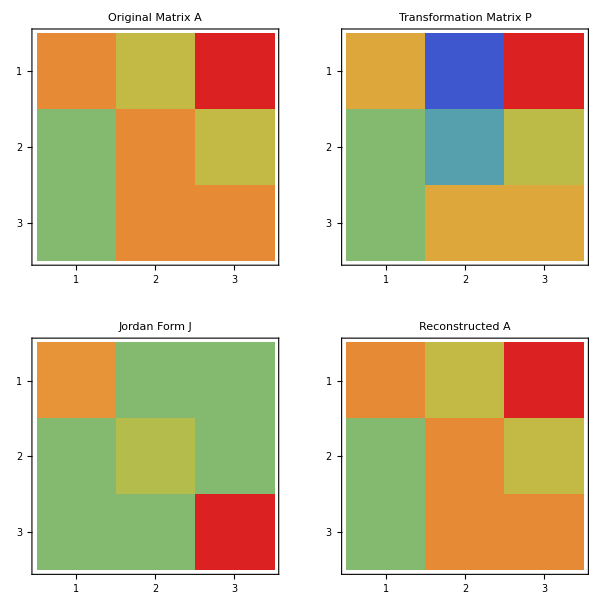

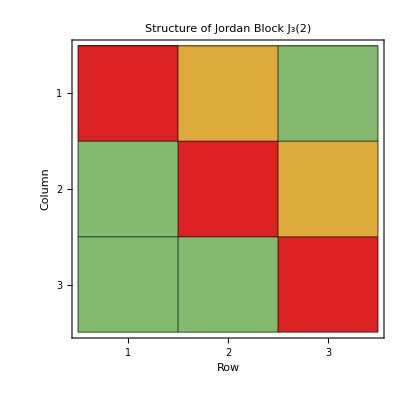

```mathematica
(*Visualization of the Jordan decomposition*)
GraphicsGrid[{{MatrixPlot[A,ColorFunction->"Rainbow",PlotLabel->"Original Matrix A"],MatrixPlot[P,ColorFunction->"Rainbow",PlotLabel->"Transformation Matrix P"]},{MatrixPlot[J,ColorFunction->"Rainbow",PlotLabel->"Jordan Form J"],MatrixPlot[P.J.Inverse[P],ColorFunction->"Rainbow",PlotLabel->"Reconstructed A"]}},ImageSize->600]

(*Visualizing Jordan block structure*)
Block[{size=3,λ=2},jordanBlock=SparseArray[{{i_,i_}->λ,{i_,j_}/;j==i+1->1},{size,size}];
MatrixPlot[jordanBlock,ColorFunction->"Rainbow",PlotLabel->"Structure of Jordan Block J₃(2)",Mesh->All,MeshStyle->Directive[Black,Opacity[0.5]],FrameLabel->{{"Row",None},{"Column",None}}]]
```

## Polar Decomposition

The Polar decomposition is analogous to expressing a complex number in polar form. For matrices, any square matrix  can be decomposed as:


where:

is a unitary matrix.

is a positive semidefinite Hermitian matrix.

For real matrices,  is orthogonal and  is symmetric positive semidefinite. The decomposition is unique if  is invertible, in which case  is positive definite. 

The polar decomposition has a clear geometric interpretation:  represents a scaling/stretching along its eigenvector directions, while  represents a rotation. This connection to physical transformations makes the polar decomposition particularly useful in applications like computer graphics, continuum mechanics and quantum physics.

The factors can be computed through the singular value decomposition (SVD) which we’ve dealt with in the previous notebook.
Given  then  and .

```mathematica
PolarDecomposition[A_]:=Module[{U, P, W, V, Sigma},
{W,Sigma,V}=SingularValueDecomposition[A];
U=W.ConjugateTranspose[V];
P=V.DiagonalMatrix[Diagonal[Sigma]].ConjugateTranspose[V];
{U//FullSimplify,P//FullSimplify}
]
(*Create a sample matrix*)
A={{3,1},{0,4}};
MatrixForm[A]

(*Compute the polar decomposition*)
{U,P}=PolarDecomposition[A];

(*Display the factors*)
Print["Unitary/Orthogonal factor U:"]
MatrixForm[U]
Print["Positive semidefinite factor P:"]
MatrixForm[P]

(*Verification*)
Print["Verification: A = U.P"]
U.P==A
Print["Difference:"]
MatrixForm[U.P-A//Chop]

(*Verify properties*)
Print["Is U orthogonal? ",Chop[Transpose[U].U-IdentityMatrix[2]]==ConstantArray[0,{2,2}]]
Print["Is P symmetric? ",Chop[P-Transpose[P]]==ConstantArray[0,{2,2}]]
Print["Is P positive semidefinite? ",And@@(#>=0&/@Eigenvalues[P])]
```

(3 | 1
0 | 4)

Unitary/Orthogonal factor U:

(7/(5 √2) | 1/(5 √2)
-1/(5 √2) | 7/(5 √2))

Positive semidefinite factor P:

(21/(5 √2) | 3/(5 √2)
3/(5 √2) | 29/(5 √2))

Verification: A = U.P

True

Difference:

(0 | 0
0 | 0)

Is U orthogonal? True

Is P symmetric? True

Is P positive semidefinite? True

### Visualization

-Graphics-

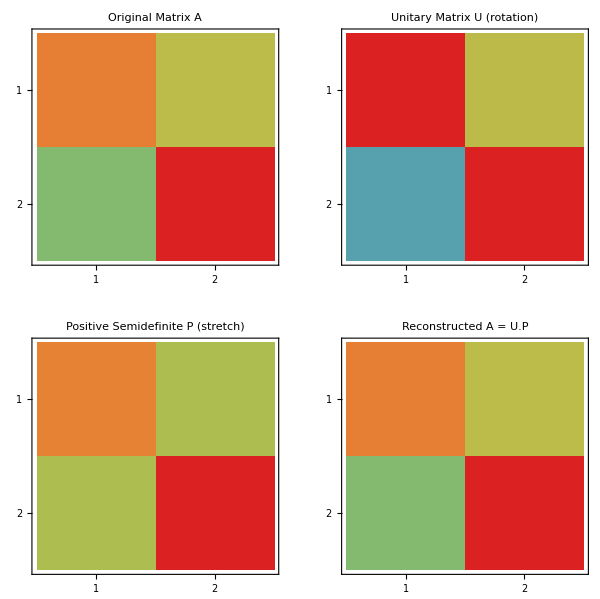

```mathematica
(*Visualization of polar decomposition's geometric interpretation*)(*First,we'll create a unit circle and transform it with A,U,and P*)
unitCircle=Table[{Cos[θ],Sin[θ]},{θ,0,2π,π/20}];
circleTransformedByA=Map[A.#&,unitCircle];
circleTransformedByU=Map[U.#&,unitCircle];
circleTransformedByP=Map[P.#&,unitCircle];

(*Plotting the transformations*)
Graphics[{{Thickness[0.005],Gray,Line[unitCircle]},(*Original circle*){Thickness[0.005],Red,Line[circleTransformedByA]},(*Transformed by A*){Thickness[0.005],Blue,Line[circleTransformedByU]},(*Rotated by U*){Thickness[0.005],Green,Line[circleTransformedByP]},(*Stretched by P*){Black,Arrow[{{0,0},{1,0}}]},(*x-axis*){Black,Arrow[{{0,0},{0,1}}]}  (*y-axis*)},PlotRange->{{-5,5},{-5,5}},PlotLabel->"Geometric Interpretation of Polar Decomposition",Epilog->{Text["Original",{1.2,0.2}],Text["A",{Sequence@@circleTransformedByA[[10]]}],Text["U (rotation)",{Sequence@@circleTransformedByU[[10]]}],Text["P (stretch)",{Sequence@@circleTransformedByP[[10]]}]},Axes->True,AxesLabel->{"x","y"},AspectRatio->1,ImageSize->500]

(*Matrix heat maps*)
GraphicsGrid[{{MatrixPlot[A,ColorFunction->"Rainbow",PlotLabel->"Original Matrix A"],MatrixPlot[U,ColorFunction->"Rainbow",PlotLabel->"Unitary Matrix U (rotation)"]},{MatrixPlot[P,ColorFunction->"Rainbow",PlotLabel->"Positive Semidefinite P (stretch)"],MatrixPlot[U.P,ColorFunction->"Rainbow",PlotLabel->"Reconstructed A = U.P"]}},ImageSize->600]
```

## Generalized Inverse (Moore-Penrose Inverse)

The Moore-Penrose inverse (or pseudoinverse) extends the concept of matrix inversion to non-square and singular matrices. For any matrix , the Moore-Penrose inverse  is the unique matrix satisfying all four Moore-Penrose conditions:

, and  (reflexivity).

, and  (, and  are Hermitian)

The Moore-Penrose inverse has numerous applications:

Least squares solutions: For an overdetermined system  gives the minimum norm least squares solution.

Rank determination: the rank of  equals the rank of .

Matrix decomposition: It’s closely related to the SVD.

Low-rank approximations: Used in principal component analysis and image compression.

For a matrix with full column rank, the pseudoinverse simplifies to , which is the left inverse. And for a matrix with full row rank. the pseudoinverse simplifies to  which is the right inverse. The pseudoinverse can be computed using the Singular Value Decomposition (SVD);

Given , then  where  is formed by taking the reciprocal of each non-zero singular value and transposing the resulting matrix.

```mathematica
(*Create a non-square matrix*)
A={{1,2,3},{4,5,6}};
MatrixForm[A]

(*Compute the Moore-Penrose inverse*)
Aplus=PseudoInverse[A];
Print["Moore-Penrose inverse:"]
MatrixForm[Aplus]

(*Verify the four Moore-Penrose conditions*)
Print["Checking Moore-Penrose conditions:"]
Print["1. A·A⁺·A = A? ",Chop[A.Aplus.A-A]==ConstantArray[0,Dimensions[A]]]
Print["2. A⁺·A·A⁺ = A⁺? ",Chop[Aplus.A.Aplus-Aplus]==ConstantArray[0,Dimensions[Aplus]]]
Print["3. (A·A⁺)* = A·A⁺? ",Chop[ConjugateTranspose[A.Aplus]-A.Aplus]==ConstantArray[0,{2,2}]]
Print["4. (A⁺·A)* = A⁺·A? ",Chop[ConjugateTranspose[Aplus.A]-Aplus.A]==ConstantArray[0,{3,3}]]

(*Compute via SVD*)
{U,Σ,V}=SingularValueDecomposition[A];
(*Create Σ⁺ by inverting non-zero singular values and transposing*)
ΣPlus=SparseArray[{i_,i_}/;Σ[[i,i]]!=0->1/Σ[[i,i]],Dimensions[Transpose[Σ]]];
AplusViaSVD=V.ΣPlus.ConjugateTranspose[U];
Print["Pseudoinverse via SVD:"]
MatrixForm[AplusViaSVD]
Print["Difference with direct computation:"]
MatrixForm[Aplus-AplusViaSVD//Chop]

(*Solve an overdetermined system using pseudoinverse*)
b={10,28};
Print["Solving overdetermined system Ax = b:"]
x=Aplus.b;
Print["Least squares solution x:"]
x
Print["Verification: Ax ≈ b? "]
A.x
Print["Residual norm ||Ax - b||: ",Norm[A.x-b]]
```

(1 | 2 | 3
4 | 5 | 6)

Moore-Penrose inverse:

(-17/18 | 4/9
-1/9 | 1/9
13/18 | -2/9)

Checking Moore-Penrose conditions:

1. A·A⁺·A = A? True

2. A⁺·A·A⁺ = A⁺? True

3. (A·A⁺)* = A·A⁺? True

4. (A⁺·A)* = A⁺·A? True

Part::pkspec1: The expression i cannot be used as a part specification.

Pseudoinverse via SVD:

(((-63-√8065) (4+1/64 (-63-√8065)))/(32 √(2 (91-√8065) (1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)))+((-63+√8065) (4+1/64 (-63+√8065)))/(32 √(2 (91+√8065) (1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2))) | (4+1/64 (-63-√8065)) √(2/((91-√8065) (1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)))+(4+1/64 (-63+√8065)) √(2/((91+√8065) (1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)))
((-63-√8065) (5+1/32 (-63-√8065)))/(32 √(2 (91-√8065) (1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)))+((-63+√8065) (5+1/32 (-63+√8065)))/(32 √(2 (91+√8065) (1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2))) | (5+1/32 (-63-√8065)) √(2/((91-√8065) (1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)))+(5+1/32 (-63+√8065)) √(2/((91+√8065) (1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)))
((-63-√8065) (6+3/64 (-63-√8065)))/(32 √(2 (91-√8065) (1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)))+((-63+√8065) (6+3/64 (-63+√8065)))/(32 √(2 (91+√8065) (1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2))) | (6+3/64 (-63-√8065)) √(2/((91-√8065) (1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)))+(6+3/64 (-63+√8065)) √(2/((91+√8065) (1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2))))

Difference with direct computation:

(-17/18-((-63-√8065) (4+1/64 (-63-√8065)))/(32 √(2 (91-√8065) (1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)))-((-63+√8065) (4+1/64 (-63+√8065)))/(32 √(2 (91+√8065) (1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2))) | 4/9-(4+1/64 (-63-√8065)) √(2/((91-√8065) (1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)))-(4+1/64 (-63+√8065)) √(2/((91+√8065) (1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)))
-1/9-((-63-√8065) (5+1/32 (-63-√8065)))/(32 √(2 (91-√8065) (1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)))-((-63+√8065) (5+1/32 (-63+√8065)))/(32 √(2 (91+√8065) (1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2))) | 1/9-(5+1/32 (-63-√8065)) √(2/((91-√8065) (1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)))-(5+1/32 (-63+√8065)) √(2/((91+√8065) (1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2)))
13/18-((-63-√8065) (6+3/64 (-63-√8065)))/(32 √(2 (91-√8065) (1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)))-((-63+√8065) (6+3/64 (-63+√8065)))/(32 √(2 (91+√8065) (1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2))) | -2/9-(6+3/64 (-63-√8065)) √(2/((91-√8065) (1+(-63-√8065)^2/4096) ((4+1/64 (-63-√8065))^2+(5+1/32 (-63-√8065))^2+(6+3/64 (-63-√8065))^2)))-(6+3/64 (-63+√8065)) √(2/((91+√8065) (1+(-63+√8065)^2/4096) ((4+1/64 (-63+√8065))^2+(5+1/32 (-63+√8065))^2+(6+3/64 (-63+√8065))^2))))

Solving overdetermined system Ax = b:

Least squares solution x:

{3,2,1}

Verification: Ax ≈ b?

{10,28}

Residual norm ||Ax - b||: 0

### Visualization

-Graphics3D-

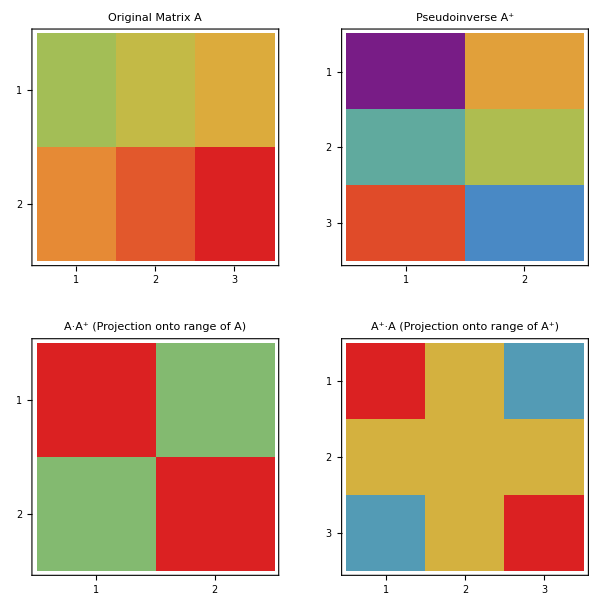

```mathematica
(*Visualize the action of a matrix and its pseudoinverse*)(*Let's create a simple example in 2D to 3D and back*)
A2={{1,0},{0,2},{1,1}};  (*3×2 matrix mapping R.b2->R.b3*)
A2plus=PseudoInverse[A2];     (*2×3 pseudoinverse mapping R.b3->R.b2*)

(*Create points in R.b2*)
points2D=Table[{Cos[t],Sin[t]},{t,0,2π,π/8}];

(*Map to R.b3*)
points3D=Map[A2.#&,points2D];

(*Map back with pseudoinverse*)
pointsRecovered=Map[A2plus.#&,points3D];

(*Visualize*)
Graphics3D[{{Red,PointSize[0.02],Point[Map[Append[#,0]&,points2D]]},(*Original in xy-plane*){Blue,PointSize[0.02],Point[points3D]},(*Mapped to 3D*){Green,PointSize[0.02],Point[Map[Append[#,0]&,pointsRecovered]]},(*Recovered in xy-plane*){Opacity[0.3],Gray,InfinitePlane[{{0,0,0},{1,0,0},{0,1,0}}]} (*xy-plane*)},PlotLabel->"Action of A and A⁺",Boxed->True,Axes->True,AxesLabel->{"x","y","z"},ViewPoint->{1.3,-2.4,2.0},Background->White,ImageSize->500]

(*Matrix heat maps*)
GraphicsGrid[{{MatrixPlot[A,ColorFunction->"Rainbow",PlotLabel->"Original Matrix A"],MatrixPlot[Aplus,ColorFunction->"Rainbow",PlotLabel->"Pseudoinverse A⁺"]},{MatrixPlot[A.Aplus,ColorFunction->"Rainbow",PlotLabel->"A·A⁺ (Projection onto range of A)"],MatrixPlot[Aplus.A,ColorFunction->"Rainbow",PlotLabel->"A⁺·A (Projection onto range of A⁺)"]}},ImageSize->600]
```

## Matrix Functions

Matrix functions extend scalar functions to matrices, allowing us to compute expressions like , or  for matrices. These functions are defined for any square matrix and have important applications in differential equations, dynamical systems, quantum mechanics, and many other fields. The most general approach to defining matrix functions uses the Jordan canonical form. For a matrix  with Jordan decomposition , we define:
.

Since  is block diagonal, computing  reduces to computing the function on each Jordan block. For a Jordan block , the function is applied as:

-Graphics- (Sorry Mathematica had problem rendering it)

For diagonalizable matrices, where  with D diagonal, the formula simplifies to:



where  is the diagonal matrix with entries .

## Matrix Exponential

The matrix exponential is one of the most important matrix functions, with applications in solving systems of differential equations, continuous-time Markov chains, and Lie group theory. For a square matrix A, the matrix exponential is defined using the power series:

Key properties of the matrix exponential include:

=  if and only if  (matrices commute)

If  is diagonalizable as A, then  where  is a diagonal matrix

For any square matrix,

is always invertible with

The matrix exponential is especially important for solving systems of first-order linear differential equations:
; whose solution is .

```mathematica
(* Create a simple 2×2 matrix *)
A = {{0, 1}, {-1, 0}};
Print["Matrix A:"]
MatrixForm[A]

(* Compute the matrix exponential *)
expA = MatrixExp[A];
Print["Matrix exponential e^A:"]
MatrixForm[expA]

(* Compute using power series approximation (for demonstration) *)
powerSeriesExp[mat_, terms_] := 
  Sum[MatrixPower[mat, k]/Factorial[k], {k, 0, terms}];
  
expA_series = powerSeriesExp[A, 10];
Print["e^A via power series (10 terms):"]
MatrixForm[expA_series]
Print["Difference with direct computation:"]
MatrixForm[expA - expA_series // Chop]

(* For this particular matrix, e^A represents a rotation *)
(* Let's verify by applying it to some vectors *)
v = {1, 0};
expA.v // N
(* This should be approximately {0, 1}, a 90° rotation *)

(* Solving a differential equation system *)
Print["Solving differential equation x'(t) = Ax:"]
Print["Initial condition x(0) = {1, 0}"]
Print["Solution at t = π/2:"]
MatrixExp[A * (Pi/2)].{1, 0} // N
(* Should be approximately {0, 1}, a 90° rotation *)

(* Verify properties *)
Print["Properties of matrix exponential:"]
Print["det(e^A) = ", Det[expA] // N]
Print["e^tr(A) = ", Exp[Tr[A]] // N]
Print["(e^A)^(-1) = e^(-A)? ", 
  Norm[Inverse[expA] - MatrixExp[-A]] < 10^-10]
```

Matrix A:

(0 | 1
-1 | 0)

Matrix exponential e^A:

(Cos[1] | Sin[1]
-Sin[1] | Cos[1])

e^A via power series (10 terms):

expA_series

Difference with direct computation:

(Cos[1]-expA_series | -expA_series+Sin[1]
-expA_series-Sin[1] | Cos[1]-expA_series)

{0.540302,-0.841471}

Solving differential equation x'(t) = Ax:

Initial condition x(0) = {1, 0}

Solution at t = π/2:

{0.,-1.}

Properties of matrix exponential:

det(e^A) = 1.

e^tr(A) = 1.

(e^A)^(-1) = e^(-A)? True

### Visualization

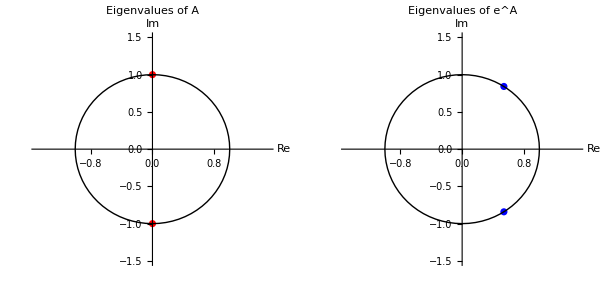

```mathematica
(* Visualize action of matrix exponential for different values of t *)
tValues = Range[0, 2π,0.1];
unitCircle = Table[{Cos[θ], Sin[θ]}, {θ, 0, 2π, π/20}];

(* Create frames for animation *)
frames = Table[
  Graphics[{
    {Thickness[0.005], LightGray, Line[unitCircle]}, (* Unit circle *)
    {Thickness[0.002], Dashed, Gray, 
     Line[{{0, 0}, {Cos[t], Sin[t]}}]}, (* Radius at angle t *)
    {Red, Arrow[{{0, 0}, {1, 0}}]}, (* Initial vector *)
    {Blue, Arrow[{{0, 0}, MatrixExp[A*t].{1, 0}}]}, (* Rotated vector *)
    {Black, Arrow[{{0, 0}, {1, 0}}]}, (* x-axis *)
    {Black, Arrow[{{0, 0}, {0, 1}}]}  (* y-axis *)
  },
  PlotRange -> {{-1.2, 1.2}, {-1.2, 1.2}},
  PlotLabel -> StringForm["e^(At) for t = ``", NumberForm[t, {3, 2}]],
  Axes -> True,
  AxesLabel -> {"x", "y"},
  AspectRatio -> 1,
  ImageSize -> 400], 
  {t, tValues}];

(* Display animation *)
ListAnimate[frames]

(* Visualize eigenvalues of A and e^A *)
eigenA = Eigenvalues[A];
eigenExpA = Eigenvalues[expA];

GraphicsGrid[{
  {ListPlot[ReIm[eigenA], PlotLabel -> "Eigenvalues of A", 
    AxesLabel -> {"Re", "Im"}, PlotStyle -> Red, 
    PlotRange -> {{-1.5, 1.5}, {-1.5, 1.5}}, AspectRatio -> 1,
    Epilog -> {Circle[{0, 0}, 1, {0, 2π}]}],
   ListPlot[ReIm[eigenExpA], PlotLabel -> "Eigenvalues of e^A", 
    AxesLabel -> {"Re", "Im"}, PlotStyle -> Blue, 
    PlotRange -> {{-1.5, 1.5}, {-1.5, 1.5}}, AspectRatio -> 1,
    Epilog -> {Circle[{0, 0}, 1, {0, 2π}]}]}
}, ImageSize -> 600]
```

## Logarithms and Matrix Sparse Roots

The matrix logarithm is the inverse of the matrix exponential . For a nonsingular matrix , the principal matrix logarithm  is the unique matrix  such that  and the eigenvalues of  lie within the strip  . Similarly, the principal square root of a matrix , denoted  or , is the unique matrix  such that  and the eigenvalues of  have positive real parts (when possible) . Both functions are well - defined for matrices with no eigenvalues on the negative real axis (for the logarithm) or zero (for the square root).

For a diagonalizable matrix :

where  applies the scalar logarithm to diagonal entries.

where  applies the scalar square root to diagonal entries

For non-diagonalizable matrices, the computation is more involved and requires the Jordan canonical form. Applications include solving matrix equations, computing fractional powers of matrices, and stability analysis of dynamical systems.

```mathematica
(* Create a positive definite matrix *)
A = {{4, 1}, {1, 3}};
Print["Matrix A:"]
MatrixForm[A]

(* Compute the matrix logarithm *)
logA = MatrixLog[A];
Print["Matrix logarithm log(A):"]
MatrixForm[logA]

(* Verify e^(log(A)) = A *)
Print["Verification: e^(log(A)) = A?"]
MatrixForm[MatrixExp[logA]]
Print["Difference:"]
MatrixForm[MatrixExp[logA] - A // Chop]

(* Compute the matrix square root *)
sqrtA = MatrixPower[A, 1/2];
Print["Matrix square root A^(1/2):"]
MatrixForm[sqrtA]

(* Verify (A^(1/2))^2 = A *)
Print["Verification: (A^(1/2))^2 = A?"]
MatrixForm[sqrtA.sqrtA]
Print["Difference:"]
MatrixForm[sqrtA.sqrtA - A // Chop]

(* Computing other matrix powers *)
Print["Computing A^(3/4):"]
MatrixForm[MatrixPower[A, 3/4]]

(* Connection between logarithm and square root *)
Print["log(A) vs 2*log(A^(1/2)):"]
Print["Difference:"]
MatrixForm[logA - 2*MatrixLog[sqrtA] // Chop]
```

Matrix A:

(4 | 1
1 | 3)

Matrix logarithm log(A):

(-((1-√5) Log[1/2 (7-√5)])/(2 √5)+((1+√5) Log[1/2 (7+√5)])/(2 √5) | -((-1-√5) (1-√5) Log[1/2 (7-√5)])/(4 √5)-((1-√5) (1+√5) Log[1/2 (7+√5)])/(4 √5)
-Log[1/2 (7-√5)]/(√5)+Log[1/2 (7+√5)]/(√5) | -((-1-√5) Log[1/2 (7-√5)])/(2 √5)-((1-√5) Log[1/2 (7+√5)])/(2 √5))

Verification: e^(log(A)) = A?

(((7+√5) (Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]-Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)]))-((-7+√5) (-Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]+Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)])) | ((-7+√5) (-1+√5) (1+√5))/(8 √5)+((-1+√5) (1+√5) (7+√5))/(8 √5)
((-7+√5) (√5 Log[1/2 (7-√5)]-√5 Log[1/2 (7+√5)]))/(10 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)]))+((7+√5) (√5 Log[1/2 (7-√5)]-√5 Log[1/2 (7+√5)]))/(10 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)])) | -((-7+√5) (Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]-Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)]))+((7+√5) (-Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]+Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)])))

Difference:

(-4+((7+√5) (Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]-Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)]))-((-7+√5) (-Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]+Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)])) | -1+((-7+√5) (-1+√5) (1+√5))/(8 √5)+((-1+√5) (1+√5) (7+√5))/(8 √5)
-1+((-7+√5) (√5 Log[1/2 (7-√5)]-√5 Log[1/2 (7+√5)]))/(10 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)]))+((7+√5) (√5 Log[1/2 (7-√5)]-√5 Log[1/2 (7+√5)]))/(10 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)])) | -3-((-7+√5) (Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]-Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)]))+((7+√5) (-Log[1/2 (7-√5)]+√5 Log[1/2 (7-√5)]+Log[1/2 (7+√5)]-√5 Log[1/2 (7+√5)]))/(4 √5 (Log[1/2 (7-√5)]-Log[1/2 (7+√5)])))

Matrix square root A^(1/2):

(1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5)) | -1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5))
-√(1/10 (7-√5))+√(1/10 (7+√5)) | 1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5)))

Verification: (A^(1/2))^2 = A?

((1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5)))^2+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5))) | (1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5)))+(1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5)))
(-√(1/10 (7-√5))+√(1/10 (7+√5))) (1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5)))+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5))) | (1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5)))^2+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5))))

Difference:

(-4+(1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5)))^2+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5))) | -1+(1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5)))+(1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5)))
-1+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5)))+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (1/2 √(1/10 (7-√5)) (-1+√5)+1/2 (1+√5) √(1/10 (7+√5))) | -3+(1/2 √(1/10 (7-√5)) (1+√5)+1/2 (-1+√5) √(1/10 (7+√5)))^2+(-√(1/10 (7-√5))+√(1/10 (7+√5))) (-1/4 √(1/10 (7-√5)) (-1+√5) (1+√5)+1/4 (-1+√5) (1+√5) √(1/10 (7+√5))))

Computing A^(3/4):

(((7-√5)^(3/4) (-1+√5))/(2 2^(3/4) √5)+((1+√5) (7+√5)^(3/4))/(2 2^(3/4) √5) | -((1/2 (7-√5))^(3/4) (-1+√5) (1+√5))/(4 √5)+((-1+√5) (1+√5) (1/2 (7+√5))^(3/4))/(4 √5)
-(7-√5)^(3/4)/(2^(3/4) √5)+(7+√5)^(3/4)/(2^(3/4) √5) | ((7-√5)^(3/4) (1+√5))/(2 2^(3/4) √5)+((-1+√5) (7+√5)^(3/4))/(2 2^(3/4) √5))

log(A) vs 2*log(A^(1/2)):

Difference:

(-((1-√5) Log[1/2 (7-√5)])/(2 √5)+((1+√5) Log[1/2 (7+√5)])/(2 √5)-2 (((√(10 (7-√5))-√(10 (7+√5))+10 √(7-2 √11)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))-2 √(7-2 √11))])/(20 √(7-2 √11))-((√(10 (7-√5))-√(10 (7+√5))-10 √(7-2 √11)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))+2 √(7-2 √11))])/(20 √(7-2 √11))) | -((-1-√5) (1-√5) Log[1/2 (7-√5)])/(4 √5)-((1-√5) (1+√5) Log[1/2 (7+√5)])/(4 √5)-2 (-((√(10 (7-√5))-√(10 (7+√5))-10 √(7-2 √11)) (√(10 (7-√5))-√(10 (7+√5))+10 √(7-2 √11)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))-2 √(7-2 √11))])/(40 √(10 (7-2 √11)) (√(7-√5)-√(7+√5)))+((√(10 (7-√5))-√(10 (7+√5))-10 √(7-2 √11)) (√(10 (7-√5))-√(10 (7+√5))+10 √(7-2 √11)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))+2 √(7-2 √11))])/(40 √(10 (7-2 √11)) (√(7-√5)-√(7+√5))))
-Log[1/2 (7-√5)]/(√5)+Log[1/2 (7+√5)]/(√5)-2 (((√(7-√5)-√(7+√5)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))-2 √(7-2 √11))])/(√(10 (7-2 √11)))-((√(7-√5)-√(7+√5)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))+2 √(7-2 √11))])/(√(10 (7-2 √11)))) | -((-1-√5) Log[1/2 (7-√5)])/(2 √5)-((1-√5) Log[1/2 (7+√5)])/(2 √5)-2 (-((√(10 (7-√5))-√(10 (7+√5))-10 √(7-2 √11)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))-2 √(7-2 √11))])/(20 √(7-2 √11))+((√(10 (7-√5))-√(10 (7+√5))+10 √(7-2 √11)) Log[1/4 (√(14-2 √5)+√(2 (7+√5))+2 √(7-2 √11))])/(20 √(7-2 √11))))

### Visualization

-Graphics-

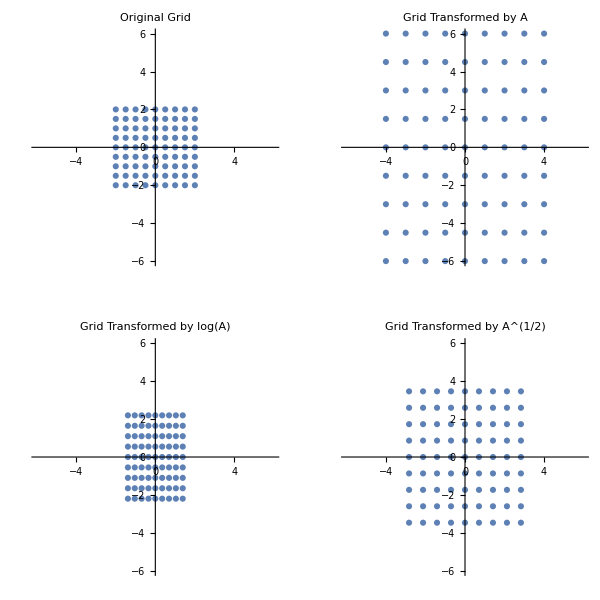

```mathematica
(* Visualize the spectral mapping between A, log(A), and sqrt(A) *)
eigenA = Eigenvalues[A];
eigenLogA = Eigenvalues[logA];
eigenSqrtA = Eigenvalues[sqrtA];

GraphicsGrid[{
  {ListPlot[eigenA, PlotLabel -> "Eigenvalues of A", 
    AxesLabel -> {"Re", "Im"}, PlotStyle -> Red],
   ListPlot[eigenLogA, PlotLabel -> "Eigenvalues of log(A)", 
    AxesLabel -> {"Re", "Im"}, PlotStyle -> Blue]},
  {ListPlot[eigenSqrtA, PlotLabel -> "Eigenvalues of A^(1/2)", 
    AxesLabel -> {"Re", "Im"}, PlotStyle -> Green],
   ListPlot[{eigenA, Map[#^(1/2) &, eigenA]}, 
    PlotLabel -> "λ vs λ^(1/2)", PlotStyle -> {Red, Green},
    AxesLabel -> {"Re", "Im"}, 
    PlotLegends -> {"λ(A)", "λ(A)^(1/2)"}]}
}, ImageSize -> 600]

(* Visualizing the action of matrix logarithm and square root *)
(* We'll use a simpler matrix for better visualization *)
B = {{2, 0}, {0, 3}};
logB = MatrixLog[B];
sqrtB = MatrixPower[B, 1/2];

(* Create a grid of points *)
grid = Flatten[Table[{x, y}, {x, -2, 2, 0.5}, {y, -2, 2, 0.5}], 1];

(* Transform grid with B, log(B), and sqrt(B) *)
gridB = Map[B.# &, grid];
gridLogB = Map[logB.# &, grid];
gridSqrtB = Map[sqrtB.# &, grid];

(* Plot transformations *)
GraphicsGrid[{
  {ListPlot[grid, PlotLabel -> "Original Grid", 
    AspectRatio -> 1, PlotRange -> {{-6, 6}, {-6, 6}}],
   ListPlot[gridB, PlotLabel -> "Grid Transformed by A", 
    AspectRatio -> 1, PlotRange -> {{-6, 6}, {-6, 6}}]},
  {ListPlot[gridLogB, PlotLabel -> "Grid Transformed by log(A)", 
    AspectRatio -> 1, PlotRange -> {{-6, 6}, {-6, 6}}],
   ListPlot[gridSqrtB, PlotLabel -> "Grid Transformed by A^(1/2)", 
    AspectRatio -> 1, PlotRange -> {{-6, 6}, {-6, 6}}]}
}, ImageSize -> 600]
```

## Functional Calculus For Matrices

The functional calculus provides a systematic framework for defining functions of matrices beyond basic operations like logarithms and square roots . It allows us to apply virtually any well - behaved function to a matrix. For any function f that is analytic on and inside a contour \Gamma enclosing all eigenvalues of A, we can define f(A) using the Cauchy integral formula:

.

This definition agrees with the power series definition when  can be represented as a power series. Another approach uses the spectral decomposition. For a diagonalizable matrix  with eigen-decomposition , where  are the spectral projectors, we define: .

This approach generalizes to the case where  is not diagonalizable using the Jordan canonical form. Practical methods for computing matrix functions include:

Diagonalization: If , then

Schur decomposition: If , then .

Padé approximation: Useful for functions like  and

Scaling and squaring: Especially efficient for computing

Polynomial approximation: Using Chebyshev or Taylor series

The functional calculus is used in solving differential equations, quantum mechanics, control theory, and network analysis.

```mathematica
(* Create a matrix *)
A = {{1, 2}, {3, 4}};
Print["Matrix A:"]
MatrixForm[A]

(* Define some matrix functions using MatrixFunction *)
sinA = MatrixFunction[Sin, A];
Print["sin(A):"]
MatrixForm[sinA]

cosA = MatrixFunction[Cos, A];
Print["cos(A):"]
MatrixForm[cosA]

(* Verify the identity sin^2(A) + cos^2(A) = I *)
Print["sin^2(A) + cos^2(A):"]
MatrixForm[sinA.sinA + cosA.cosA // Chop]

(* Using Diagonalization approach *)
{eigenvalues, P} = Eigensystem[A];
Diag = DiagonalMatrix[eigenvalues];
PInv = Inverse[Transpose[P]];

(* Computing sin(A) via diagonalization *)
sinD = DiagonalMatrix[Map[Sin, eigenvalues]];
sinA_diag = P.sinD.PInv;
Print["sin(A) via diagonalization:"]
MatrixForm[sinA_diag]
Print["Difference with direct computation:"]
MatrixForm[sinA - sinA_diag // Chop]

(* Define a more complex function *)
f[x_] := Exp[-x^2] * Sin[x];
fA = MatrixFunction[f, A];
Print["f(A) = e^(-A^2) * sin(A):"]
MatrixForm[fA]

(* Computing a matrix sign function *)
signA = MatrixFunction[Sign, A];
Print["sign(A):"]
MatrixForm[signA]

(* Verify sign(A)^2 = I *)
Print["sign(A)^2:"]
MatrixForm[signA.signA // Chop]
```

Matrix A:

(1 | 2
3 | 4)

sin(A):

(-((-3-√33) Sin[1/2 (5-√33)])/(2 √33)+((-3+√33) Sin[1/2 (5+√33)])/(2 √33) | -((-3-√33) (3-√33) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Sin[1/2 (5+√33)])/(12 √33)
-√(3/11) Sin[1/2 (5-√33)]+√(3/11) Sin[1/2 (5+√33)] | -((3-√33) Sin[1/2 (5-√33)])/(2 √33)-((-3-√33) Sin[1/2 (5+√33)])/(2 √33))

cos(A):

(-((-3-√33) Cos[1/2 (5-√33)])/(2 √33)+((-3+√33) Cos[1/2 (5+√33)])/(2 √33) | -((-3-√33) (3-√33) Cos[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Cos[1/2 (5+√33)])/(12 √33)
-√(3/11) Cos[1/2 (5-√33)]+√(3/11) Cos[1/2 (5+√33)] | -((3-√33) Cos[1/2 (5-√33)])/(2 √33)-((-3-√33) Cos[1/2 (5+√33)])/(2 √33))

sin^2(A) + cos^2(A):

((-((-3-√33) Cos[1/2 (5-√33)])/(2 √33)+((-3+√33) Cos[1/2 (5+√33)])/(2 √33))^2+(-√(3/11) Cos[1/2 (5-√33)]+√(3/11) Cos[1/2 (5+√33)]) (-((-3-√33) (3-√33) Cos[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Cos[1/2 (5+√33)])/(12 √33))+(-((-3-√33) Sin[1/2 (5-√33)])/(2 √33)+((-3+√33) Sin[1/2 (5+√33)])/(2 √33))^2+(-√(3/11) Sin[1/2 (5-√33)]+√(3/11) Sin[1/2 (5+√33)]) (-((-3-√33) (3-√33) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Sin[1/2 (5+√33)])/(12 √33)) | (-((3-√33) Cos[1/2 (5-√33)])/(2 √33)-((-3-√33) Cos[1/2 (5+√33)])/(2 √33)) (-((-3-√33) (3-√33) Cos[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Cos[1/2 (5+√33)])/(12 √33))+(-((-3-√33) Cos[1/2 (5-√33)])/(2 √33)+((-3+√33) Cos[1/2 (5+√33)])/(2 √33)) (-((-3-√33) (3-√33) Cos[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Cos[1/2 (5+√33)])/(12 √33))+(-((3-√33) Sin[1/2 (5-√33)])/(2 √33)-((-3-√33) Sin[1/2 (5+√33)])/(2 √33)) (-((-3-√33) (3-√33) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Sin[1/2 (5+√33)])/(12 √33))+(-((-3-√33) Sin[1/2 (5-√33)])/(2 √33)+((-3+√33) Sin[1/2 (5+√33)])/(2 √33)) (-((-3-√33) (3-√33) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Sin[1/2 (5+√33)])/(12 √33))
(-√(3/11) Cos[1/2 (5-√33)]+√(3/11) Cos[1/2 (5+√33)]) (-((3-√33) Cos[1/2 (5-√33)])/(2 √33)-((-3-√33) Cos[1/2 (5+√33)])/(2 √33))+(-√(3/11) Cos[1/2 (5-√33)]+√(3/11) Cos[1/2 (5+√33)]) (-((-3-√33) Cos[1/2 (5-√33)])/(2 √33)+((-3+√33) Cos[1/2 (5+√33)])/(2 √33))+(-√(3/11) Sin[1/2 (5-√33)]+√(3/11) Sin[1/2 (5+√33)]) (-((3-√33) Sin[1/2 (5-√33)])/(2 √33)-((-3-√33) Sin[1/2 (5+√33)])/(2 √33))+(-√(3/11) Sin[1/2 (5-√33)]+√(3/11) Sin[1/2 (5+√33)]) (-((-3-√33) Sin[1/2 (5-√33)])/(2 √33)+((-3+√33) Sin[1/2 (5+√33)])/(2 √33)) | (-((3-√33) Cos[1/2 (5-√33)])/(2 √33)-((-3-√33) Cos[1/2 (5+√33)])/(2 √33))^2+(-√(3/11) Cos[1/2 (5-√33)]+√(3/11) Cos[1/2 (5+√33)]) (-((-3-√33) (3-√33) Cos[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Cos[1/2 (5+√33)])/(12 √33))+(-((3-√33) Sin[1/2 (5-√33)])/(2 √33)-((-3-√33) Sin[1/2 (5+√33)])/(2 √33))^2+(-√(3/11) Sin[1/2 (5-√33)]+√(3/11) Sin[1/2 (5+√33)]) (-((-3-√33) (3-√33) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Sin[1/2 (5+√33)])/(12 √33)))

sin(A) via diagonalization:

sinA_diag

Difference with direct computation:

(-sinA_diag-((-3-√33) Sin[1/2 (5-√33)])/(2 √33)+((-3+√33) Sin[1/2 (5+√33)])/(2 √33) | -sinA_diag-((-3-√33) (3-√33) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) Sin[1/2 (5+√33)])/(12 √33)
-sinA_diag-√(3/11) Sin[1/2 (5-√33)]+√(3/11) Sin[1/2 (5+√33)] | -sinA_diag-((3-√33) Sin[1/2 (5-√33)])/(2 √33)-((-3-√33) Sin[1/2 (5+√33)])/(2 √33))

f(A) = e^(-A^2) * sin(A):

(-((-3-√33) ⅇ^(-1/4 (5-√33)^2) Sin[1/2 (5-√33)])/(2 √33)+((-3+√33) ⅇ^(-1/4 (5+√33)^2) Sin[1/2 (5+√33)])/(2 √33) | -((-3-√33) (3-√33) ⅇ^(-1/4 (5-√33)^2) Sin[1/2 (5-√33)])/(12 √33)-((-3-√33) (-3+√33) ⅇ^(-1/4 (5+√33)^2) Sin[1/2 (5+√33)])/(12 √33)
-√(3/11) ⅇ^(-1/4 (5-√33)^2) Sin[1/2 (5-√33)]+√(3/11) ⅇ^(-1/4 (5+√33)^2) Sin[1/2 (5+√33)] | -((3-√33) ⅇ^(-1/4 (5-√33)^2) Sin[1/2 (5-√33)])/(2 √33)-((-3-√33) ⅇ^(-1/4 (5+√33)^2) Sin[1/2 (5+√33)])/(2 √33))

sign(A):

((-3+√33)/(2 √33)-(3+√33)/(2 √33) | -((-3-√33) (-3+√33))/(12 √33)-((3-√33) (3+√33))/(12 √33)
2 √(3/11) | -(-3-√33)/(2 √33)+(3-√33)/(2 √33))

sign(A)^2:

(((-3+√33)/(2 √33)-(3+√33)/(2 √33))^2+2 √(3/11) (-((-3-√33) (-3+√33))/(12 √33)-((3-√33) (3+√33))/(12 √33)) | (-(-3-√33)/(2 √33)+(3-√33)/(2 √33)) (-((-3-√33) (-3+√33))/(12 √33)-((3-√33) (3+√33))/(12 √33))+((-3+√33)/(2 √33)-(3+√33)/(2 √33)) (-((-3-√33) (-3+√33))/(12 √33)-((3-√33) (3+√33))/(12 √33))
2 √(3/11) (-(-3-√33)/(2 √33)+(3-√33)/(2 √33))+2 √(3/11) ((-3+√33)/(2 √33)-(3+√33)/(2 √33)) | (-(-3-√33)/(2 √33)+(3-√33)/(2 √33))^2+2 √(3/11) (-((-3-√33) (-3+√33))/(12 √33)-((3-√33) (3+√33))/(12 √33)))

### Visualization

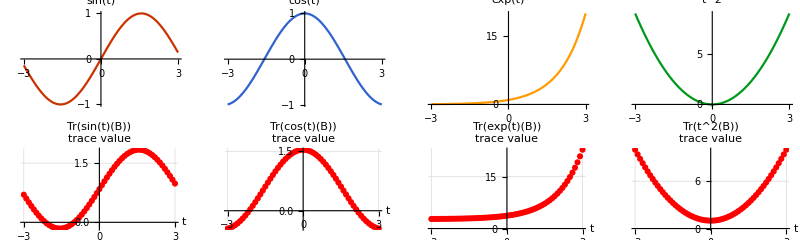

-Graphics3D-

```mathematica
(* Visualizing scalar functions vs matrix functions *)
tValues = Range[-3, 3, 0.1];
scalarFunctions = {
  Sin[#] &,
  Cos[#] &,
  Exp[#] &,
  #^2 &
};
functionNames = {"sin(t)", "cos(t)", "exp(t)", "t^2"};

(* Plot scalar functions *)
scalarPlots = Table[
  Plot[scalarFunctions[[i]][t], {t, -3, 3},
    PlotLabel -> functionNames[[i]],
    PlotStyle -> ColorData[112][i]],
  {i, 1, Length[scalarFunctions]}
];

(* Matrix B parameterized by t *)
matrixFunctionPlot[func_, name_] := Module[{B, fB, eigenvalues, trace},
  ListPlot[Table[
    B = {{1, 0}, {0, t}};  (* Diagonal matrix with eigenvalues 1 and t *)
    fB = MatrixFunction[func, B];
    eigenvalues = Eigenvalues[fB];
    trace = Tr[fB];
    {t, trace},
    {t, -3, 3, 0.1}],
    PlotLabel -> "Tr(" <> name <> "(B))",
    PlotStyle -> Red,
    AxesLabel -> {"t", "trace value"},
    GridLines -> Automatic
  ]
];

(* Generate matrix function plots *)
matrixPlots = Table[
  matrixFunctionPlot[scalarFunctions[[i]], functionNames[[i]]],
  {i, 1, Length[scalarFunctions]}
];

(* Display both types of plots *)
GraphicsGrid[{scalarPlots, matrixPlots}, ImageSize -> 800]

(* 3D visualization of matrix exponential for 2×2 matrices *)
(* We'll parameterize A = {{a, b}, {c, d}} and plot det(e^A) = e^tr(A) *)
plotPoints = Flatten[Table[
  {a, d, Exp[a + d]},
  {a, -2, 2, 0.2},
  {d, -2, 2, 0.2}
], 1];

ListPlot3D[plotPoints,
  PlotLabel -> "det(e^A) = e^tr(A) for A = {{a, b}, {c, d}}",
  AxesLabel -> {"a", "d", "det(e^A)"},
  ColorFunction -> "Rainbow",
  Mesh -> None,
  PlotRange -> All,
  ViewPoint -> {1.3, -2.4, 2.0},
  BoxRatios -> {1, 1, 1},
  ImageSize -> 500]
```

These matrix functions provide powerful tools for solving problems in differential equations, dynamical systems, quantum mechanics, and many other fields. The functional calculus framework unifies these operations and allows us to apply virtually any analytic function to matrices in a consistent and mathematically sound way.

## Structured & Sparse Matrices

## Special Structures

### Toeplitz

### Hankel

### Circulant Matrices

## Sparse

### Definition

### Storage Schemes and Efficiency

### Applications

## Extensions to Infinite-Dimensional Spaces

## Operators on Hilbert Spaces

### Bounded Operators

### Unbounded Operators

## Spectral Theorem for Unbounded Operators

## Random Matrix Theory and Bohemian Matrices

## Introduction to Random Matrix Theory

## Bohemian Matrices

## Tensor Decomposition and Multilinear Algebra

## Basics of Tensor Vs. Matrices

## Canonical Polyadic and Tucker Decomposition

## Application